## Team 5 Analyze DTMF 5 is 770Hz + 1336Hz

```mathematica
Subscript[f, 1]=770;
Subscript[f, 2]=1336;
f[t_] := Cos[2π Subscript[f, 1] t]+Cos[2 π Subscript[f, 2] t];
```

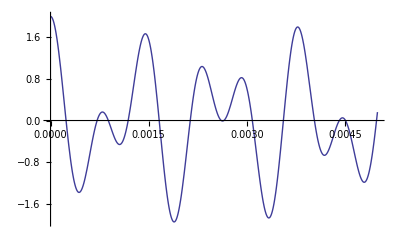

```mathematica
Plot[f[t],{t,0,1/200}]
```

For Continuous tone

```mathematica
F[ω_]:=FourierTransform[f[t],t,ωp] /. ωp->ω;
F[ω]//FullSimplify//TraditionalForm
```

√(π/2) ω-2672 π+√(π/2) ω-1540 π+√(π/2) ω+1540 π+√(π/2) ω+2672 π

For Short Pulse

```mathematica
FourierTransform[UnitBox[(t-1/2)/L],t,ωp] /. ωp->ω
```

(ⅇ^((ⅈ ω)/2) Sinc[ω/2])/(√(2 π))

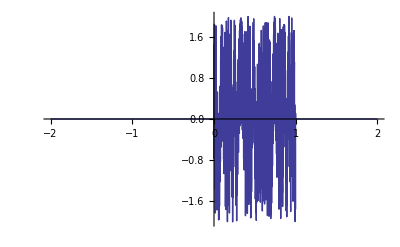

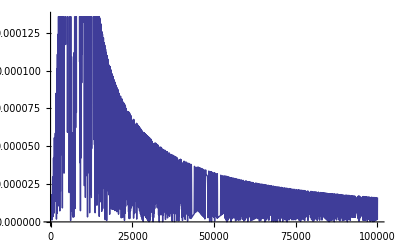

(ⅇ^((ⅈ ω)/2) (sinc(770 π-ω/2)+sinc(1336 π-ω/2)+sinc(ω/2+770 π)+sinc(ω/2+1336 π)))/(2 √(2 π))

```mathematica
L = 1;
Subscript[f, p][ω_] :=f[t]*UnitBox[(t-1/2)/L];
Subscript[F, p][ω_]:=FourierTransform[Subscript[f, p][t],t,ωp] /. ωp->ω;
Plot[Subscript[f, p][t],{t,-2,2}]
Plot[Abs[Subscript[F, p][w]]//FullSimplify//Evaluate,{w,0,100000}]
Subscript[F, p][ω]//FullSimplify//TraditionalForm
```

Sampled

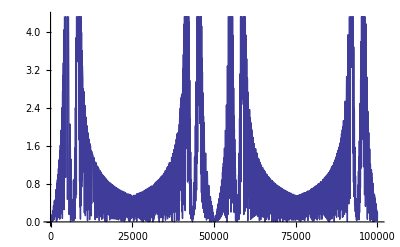

```mathematica
ws = 8000*2π;
Ts = 2π/ws;
Subscript[f, s][t_]:= f[t]*UnitBox[(t-1/2)/L];
Subscript[F, s][ω_]:=FourierTransform[Subscript[f, s][t],t,ωp]*UnitBox[ωp/ ws] /. ωp->ω;
Plot[1/Ts*Sum[Abs[Subscript[F, s][ω-n ws]],{n,-5,5}]//Evaluate,{ω,0,100000}]
```

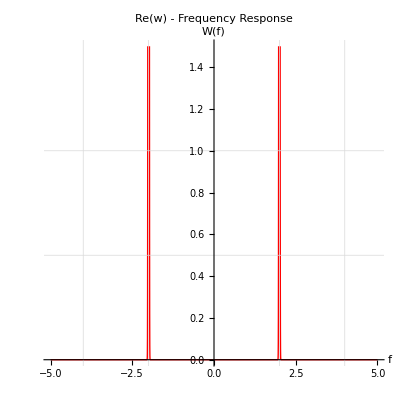

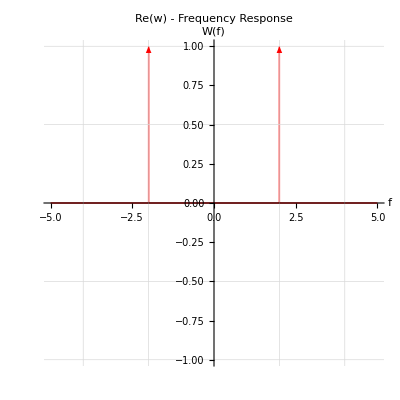

```mathematica
diracDelta[x_]=PDF[NormalDistribution[0,1/100],x];

eqn1wb:=(2 ((I Pi f) Exp[(-I) 2 Pi f]) ((1/2) DiracDelta[f-2]+DiracDelta[f+2]))/(1+I 2 Pi f);

wb1=Plot[Re[eqn1wb]/.DiracDelta->diracDelta//Evaluate,{f,-5,5},PlotStyle:>{Thick,Red},AspectRatio:>1,GridLines:>{{-4,-2,2,4},{1.0,0.5,-0.5,-1.0}},PlotLabel:>"Re(w) - Frequency Response",AxesLabel:>{"f","W(f)"},PlotRange->{Automatic,1.5}]

Plot[0,{f,-5,5},PlotStyle:>{Thick,Red},AspectRatio:>1,GridLines:>{{-4,-2,2,4},{1.0,0.5,-0.5,-1.0}},PlotLabel:>"Re(w) - Frequency Response",AxesLabel:>{"f","W(f)"},PlotRange->{Automatic,1.},Epilog->{Red,Thick,Arrow[{{-2,0},{-2,1}}],Arrow[{{2,0},{2,1}}]}]
```